```mathematica
Integrate[ Exp[-k Cos[2 ϕ]],{ϕ,0,π}]
```

π BesselI[0,k]

```mathematica
N[π BesselI[0,1]]
```

3.97746

```mathematica
FindMaximum[{Exp[-Cos[2 ϕ]],0< ϕ < π},{ϕ, 1.5}]
```

{2.71828,{ϕ→1.5708}}

```mathematica
Integrate[1/(3.97746) Exp[-Cos[2 ϕ]],{ϕ,0,ϕ0}]
```

∫_0^ϕ0 0.251417 ⅇ^(-Cos[2 ϕ])ⅆϕ

```mathematica
Cos[π]
```

-1

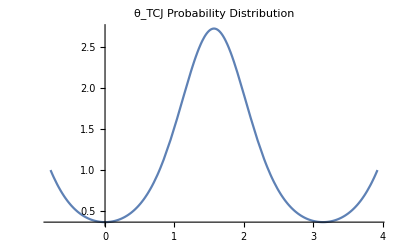

```mathematica
Plot[{Exp[-2Cos[ϕ]^2 +1]},{ϕ,-π/4,5π/4}, PlotLabel-> "θ_TCJ Probability Distribution"]
```

```mathematica
datapts = Table[{ϕ,1/(3.977463260506422)(Exp[-Cos[2ϕ]])},{ϕ, 0, 3.141, 3.141/100}];
```

Generating 100 data points for Gaussian fit.

```mathematica
NonlinearModelFit[datapts, A*Exp[-(ϕ-π/2)^2/(2σ2)] + P0, {A, μ,σ2, P0}, ϕ]
```

FittedModel[1.74843×10^7-1.74843×10^7 ⅇ^(«23» («1»)^2)]

```mathematica
Normal[%]
```

1.74843×10^7-1.74843×10^7 ⅇ^(1.38748×10^-8 (-π/2+ϕ)^2)

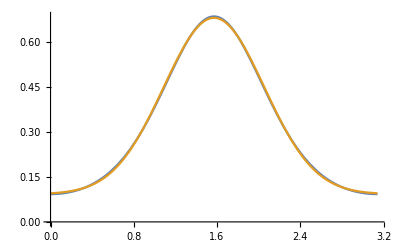

```mathematica
Plot[{1/(3.977463260506422) Exp[-Cos[2ϕ]] ,0.09210758442693216+0.5866273359249808 ⅇ^(-2.136298328298766 (-1.5707963663387658+ϕ)^2)},{ϕ,0,π}]
```

```mathematica
N[π/2]
```

1.5708

```mathematica
σsq = 1/(2*2.136298328298766)
```

0.23405

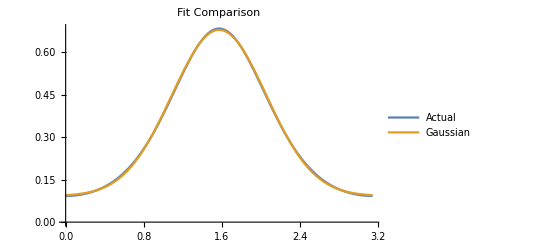

```mathematica
Plot[{1/(3.977463260506422) Exp[-Cos[2ϕ]] ,0.092107+0.586627 ⅇ^(-2.136298328298766 (-1.5707963663387658+ϕ)^2)},{ϕ,0,π}, PlotLegends-> LineLegend[{"Actual","Gaussian"}], PlotLabel->"Fit Comparison"]
```

```mathematica
Res[ϕ_]:= 1/(3.977463260506422) Exp[-Cos[2ϕ]]  - (0.092107+0.586627 ⅇ^(-2.136298328298766 (-1.5707963663387658+ϕ)^2))
```

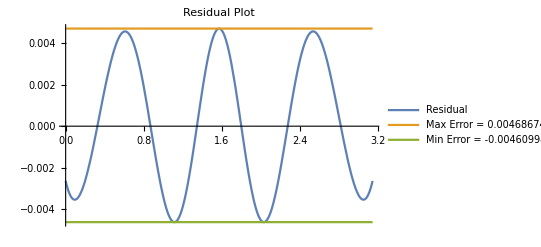

```mathematica
Plot[{Res[ϕ], 0.00469, -0.00461},{ϕ,0,π}, PlotLabel-> "Residual Plot", PlotLegends-> LineLegend[{"Residual","Max Error = 0.00468674", "Min Error = -0.00460998"} ]]
```

```mathematica
FindMaximum[{Res[ϕ], 0≤ ϕ ≤ π/2},{ϕ, 1.5}]
```

{0.00468674,{ϕ→1.56935}}

```mathematica
FindMinimum[{Res[ϕ], 0≤ ϕ ≤ π/2},{ϕ, 1.0}]
```

{-0.00460998,{ϕ→1.11303}}

Fit parameters for Gaussian: A Exp[-( x - π/2 ) / (2 σ2)] + P_0

I fitted for 3 parameters because I know that the maximum of the initial probability distribution was π/2. I also fitted for σ^2 instead of σ, just in case it made the solver’s job easier.

P_0 = 0.092107
A = 0.586627
σ^2= 0.23405

I also truncated to 6 sig figs since it did not affect the fit that much.

Untruncated Residual:

```mathematica
Res2[ϕ_] :=1/(3.977463260506422) Exp[-Cos[2ϕ]] -  0.09210758442693216-0.5866273359249808 ⅇ^(-2.136298328298766 (-1.5707963663387658+ϕ)^2)
```

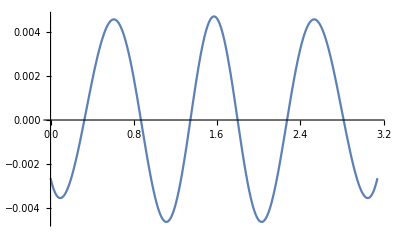

```mathematica
Plot[Res2[ϕ], {ϕ,0,π}]
```

So then, approximate P(θ-θ_TCJ):

```mathematica
P[ϕ_]:= 0.09210758442693216+0.5866273359249808 ⅇ^(-2.136298328298766 (-1.5707963663387658+ϕ)^2)
```

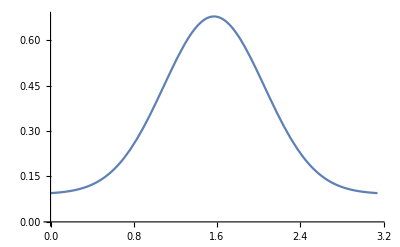

```mathematica
Plot[P[ϕ],{ϕ,0,π}]
```

```mathematica
NF =Integrate[P[ϕ],{ϕ,0,π}]
```

0.999922

New factor by which we should normalize this new distribution

```mathematica
Pn[ϕ_]:= 1/(0.999922)*(0.09210758442693216+0.5866273359249808 ⅇ^(-2.136298328298766 (-1.5707963663387658+ϕ)^2))
```

```mathematica
NF2 = Integrate[Pn[ϕ],{ϕ,0,π}]
```

1.

```mathematica
Res3[ϕ_] :=1/(3.977463260506422) Exp[-Cos[2ϕ]] -  (0.09210758442693216+0.5866273359249808 ⅇ^(-2.136298328298766 (-1.5707963663387658+ϕ)^2))*(1/0.999922)
```

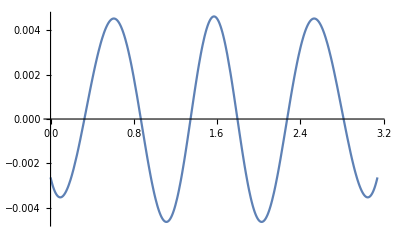

```mathematica
Plot[Res3[ϕ], {ϕ,0,π}]
```

Now in theory, if I can manipulate C++‘s normal distribution to make this distribution work, we should be good to go. The standard normal distribution does not have a constant offset however. So I should see if I can use some stats tricks to artificially construct my offset normal distribution.

Conclusion: Since C++ does not have a built in Gaussian distribution, this fitting does not amount too much. I will continue using this Mathematica Notebook to determine a good anisotropy potential

Goals: Find a potential that will allow me to control the directions of faster/ slower growth and the strength of anisotropy.

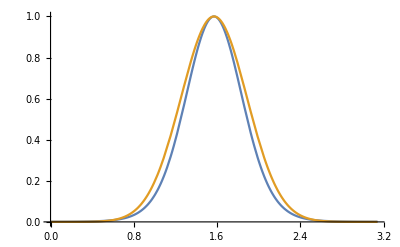

```mathematica
Plot[{Exp[-(  7Cos[θ]^2)], Exp[-5(θ-π/2)^2]},{θ,0,π}]
```

```mathematica
Integrate[Exp[-k(Cos[θ])^2],{θ,0, π}]
```

ⅇ^(-k/2) π BesselI[0,k/2]

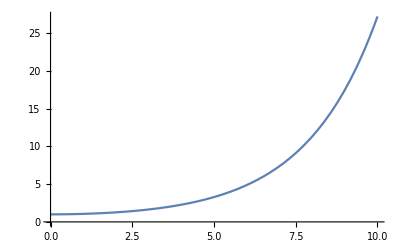

```mathematica
Plot[BesselI[0, k/2],{k,0,10}]
```

```mathematica
Integrate[Exp[-a x^2],{x,-π/2,π/2}]
```

(√π Erf[(√a π)/2])/(√a)

```mathematica
Integrate[Exp[-Cos[2x]-k Cos[x]^2],{x,0,π}]
```

∫_0^π ⅇ^(-k Cos[x]^2-Cos[2 x])ⅆx

We’re using Bessel Functions for magnetic anisotropy

```mathematica
P[k_ ,θ_]:= Exp[-(k Cos[θ]^2)] / (ⅇ^(-k/2) π BesselI[0,k/2])
```

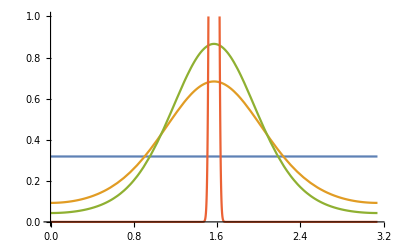

```mathematica
Plot[{P[0, θ], P[2,θ], P[3,θ], P[1000,θ]},{θ,0,π}]
```

```mathematica
P[1000,1.599]
```

8.05285

```mathematica
Integrate[P[3,θ],{θ,0,π}]
```

1

```mathematica
F[k_]:=Integrate[P[k,θ],{θ,0,π}]
```

```mathematica
F[k]
```

ⅇ^(-k/2) π BesselI[0,k/2]

```mathematica
N[BesselI[0,1/2]]
```

1.06348

```mathematica
Integrate[Exp[-Cos[2 ϕ]],{ϕ,0,π}]
```

π BesselI[0,1]

```mathematica
N[ BesselI[0,1]]
```

1.26607

```mathematica
Integrate[Exp[- k Cos[ϕ]^2],{ϕ,0,π}]
```

ⅇ^(-k/2) π BesselI[0,k/2]

```mathematica
Integrate[Exp[-Cos[2 ϕ]],{ϕ,0,π}]
```

π BesselI[0,1]

```mathematica
Integrate[Exp[-(A Sin[(2ψ)] + B Cos[(2ψ)]) ],{ψ,0,π}]
```

π BesselI[0,√(A^2+B^2)]

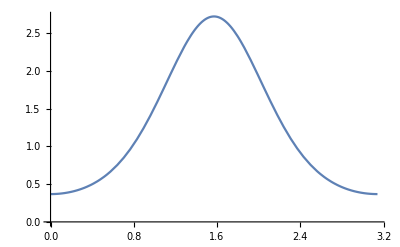

```mathematica
Plot[Exp[-Cos[2(θ - π/2)] - 2 Cos[2(θ )]],{θ,0,π}]
```

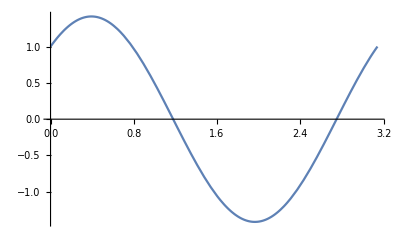

```mathematica
Plot[Cos[2(θ - ψ)] +  Sin[2(θ - α)],{θ,0,π}]
```

```mathematica
FourierSeries[Cos[2(θ - ψ)] +  Sin[2(θ - α)],θ,6]
```

1/2 ⅇ^(2 ⅈ θ) (-ⅈ ⅇ^(-2 ⅈ α)+ⅇ^(-2 ⅈ ψ))+1/2 ⅇ^(-2 ⅈ θ) (ⅈ ⅇ^(2 ⅈ α)+ⅇ^(2 ⅈ ψ))

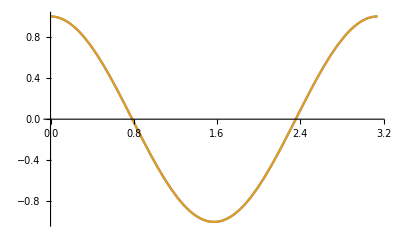

```mathematica
Plot[{Cos[2θ],Sin[2(θ-3π/4)]},{θ,0,π}]
```

```mathematica
Simplify[Cos[2(ϕ-ϕTCJ)] + k Cos[ϕ-ϕAN]^2]
```

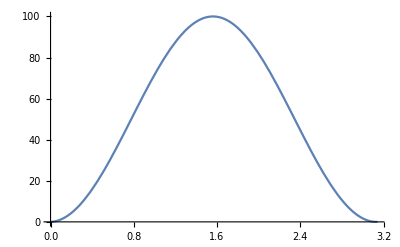

```mathematica
Plot[100 Cos[ϕ-π/2]^2+Cos[2 (ϕ-π/4)],{ϕ,0,π}]
```

```mathematica
dc[θ_] := D[k Cos[ϕ-ϕa]^2+Cos[2 (ϕ-ϕt)],ϕ]/.{ϕ-> θ}
```

```mathematica
d2c[α_]:= D[dc[θ],{θ}]/.{θ-> α}
```

```mathematica
dc[ϕ]
```

-2 k Cos[ϕ-ϕa] Sin[ϕ-ϕa]-2 Sin[2 (ϕ-ϕt)]

```mathematica
d2c[ϕ]
```

-2 k Cos[ϕ-ϕa]^2-4 Cos[2 (ϕ-ϕt)]+2 k Sin[ϕ-ϕa]^2

Solve::bdomv: Warning: ϕ>0&&ϕ<π is not a valid domain specification. Assuming it is a variable to eliminate.

Solve::ivar: ϕ>0&&ϕ<π is not a valid variable.

Solve[-2 k Cos[ϕ-ϕa] Sin[ϕ-ϕa]-2 Sin[2 (ϕ-ϕt)]==0,ϕ,ϕ>0&&ϕ<π]

```mathematica
Uc[θ_,θTCJ_, θan_, k_, k2_]:= 1/(Pi BesselI[0,Sqrt[(k2 Sin[2θTCJ] + k/2 Sin[2θan])^2 + (k2 Cos[2 θTCJ]+ k/2 Cos[2 θan])^2]])*Exp[-((k2 Cos[2 θTCJ] + k/2 Cos[2θan])Cos[2θ] + (k2 Sin[2 θTCJ]+ k/2 Sin[2 θan])Sin[2θ])]
```

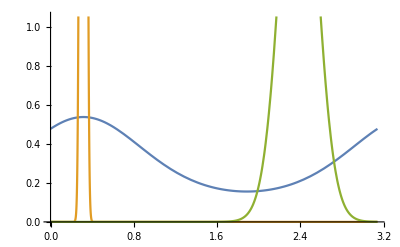

```mathematica
Plot[{Uc[θ, 2π/3,  π/4, 1, 1], Uc[θ, 2π/3, π/4, 1000, 1000], Uc[θ, 2 π/3, π/4, 20,1 ]},{θ,0,π}]
```

```mathematica
Uc2[θ_,θTCJ_, θan_, k_, k2_]:= Exp[-((k2 Cos[2 θTCJ] + k/2 Cos[2θan])Cos[2θ] + (k2 Sin[2 θTCJ]+ k/2 Sin[2 θan])Sin[2θ])]
```

Finding the maximum / upper bound of this function

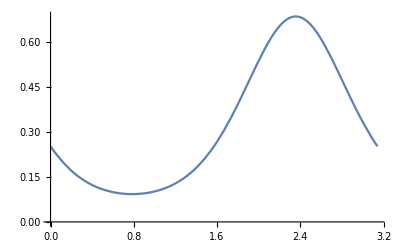

```mathematica
Plot[{Uc[θ,π/4,0,0,1]},{θ,0,π}]
```

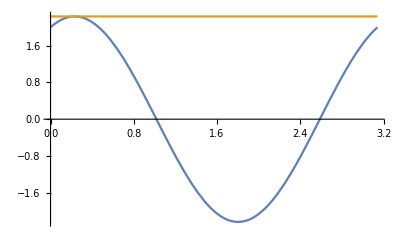

```mathematica
Plot[{2Cos[2θ] +Sin[2θ], Sqrt[5]},{θ,0,π}]
```

```mathematica
FindMaximum[-Uc[θ,π/8,π/2, 7],θ, Boole[θ>0 && θ < π]]
```

FindMaximum::vloc: The variable Boole[θ>0&&θ<π] cannot be localized so that it can be assigned to numerical values.

FindMaximum[-Uc[θ,π/8,π/2,7],θ,Boole[θ>0&&θ<π]]

```mathematica
FindMaximum[Exp[-Uc[θ,π/8,π/2,7]],Boole[θ>0&&θ<π],θ]
```

FindMaximum::vloc: The variable Boole[θ>0&&θ<π] cannot be localized so that it can be assigned to numerical values.

```mathematica
FindMaximum[Uc[θ,π/2,π/2,100],θ]
```

FindMaximum::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

{1.40935×10^22,{θ→1.11022×10^-16}}

```mathematica
Ut[θ_,θt_]:= Cos[2(θ-θt)]
```

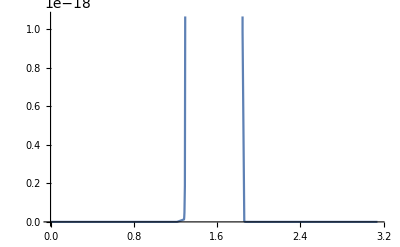

```mathematica
Plot[1/(π BesselI[0,300])Exp[-Ut[θ,0]*300],{θ,0,π}]
```

```mathematica
Integrate[Exp[-Ut[θ,θt]],{θ,0,π}]
```

π BesselI[0,1]

```mathematica
Manipulate[Plot[A Sin[θ] + B Cos[θ],{θ,0,π}],{A,0,10}, {B,0,10}]
```

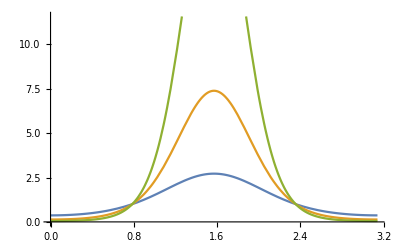

```mathematica
Plot[{Exp[-Cos[2θ]], Exp[-2 Cos[2θ]], Exp[-3 Cos[2θ]]},{θ, 0, π}]
```